# FAQ : Causal Networks

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

Causal Networks:

Currently the best description of how a causal is constructed from a sessie is in the Caviness, Beard, ________ & Deschamps paper.

Anyone want to help mine pieces of that explanation to create this FAQ?
Or to start building a nice animated explanation, similar to Jade Deschamps’ PPT in the Repo “Intro-Documents” 

From <https://github.com/orgs/sessieresearchatsau/repositories>

COLTON’S WRITING BELOW

#### Causal Networks

A causal network, also known as a Bayesian network, is a graphical model that is used to represent the relationship between two or more variables. This network typically consists of nodes, which represent variables, and edges connecting these nodes,  which represent causal influences between them. This means that any two nodes connected together will have some dependency on each other (or one node is dependant on the parent node) while two nodes not connected are independent of each other. Causal networks are different from other networks due to these lines as they indicate causality between the nodes rather than just indicating that they are associated.

```mathematica
(-Graphics-)^□
```

Figure 1: An example of a simple Bayesian network

Figure 1 is a basic example of a causal network, as indicated by the nodes (rain, sprinkler, wet grass) and the lines indicating the relationship between them. Rain has an effect on both the sprinkler (turning it off) and the wet grass (making it wet), as indicated by the arrows, while sprinklers only have an effect on wet grass. Because wet grass is only affected by the other nodes, it is strictly dependent and causes no change in the others.

#### Causality vs Correlation

When building a causal network, it is important to be able to differentiate between causation and correlation as correlation does not imply causation. In the absence of enough scientific research, it can be necessary to draw causal inferences from observational data, but doing this accurately can be challenging. While comparing variables it is necessary to differentiate between weather an event/variable actually causes a specific outcome or weather it is merely correlated. Looking back at Figure 1, we know that rain falling directly causes the grass to get wet, allowing us to conclude that there is a causal relationship between them. However, if we tried to draw a causal network between the presence of wet grass and the use of umbrellas, this would be an example of correlation and not causation. Wet grass and people using umbrellas are both effects of rain falling and are not directly affected by each other. When constructing causal networks it is important to verify that your two variables are truly affected by each other and that a confounding variable is not affecting your judgment.

#### Applications of Causal Networks

Causal networks can be useful in a variety of fields including determining the causal factors for disease in medicine, the effects of environment changes on ecosystems, developing artificial neural networks, and many other examples.

#### Causal Networks of Sequential Substitution Systems

The causal network shown for a Sessie is built from a study of which cells in the colored picture are created and destroyed by which events. The creation of a cell must precede its destruction. This is taken as a model for a causal connection of any type.



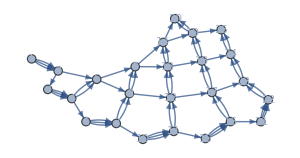
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss1 = SSS[{"ABA"->"AAB","A"->"ABA"},"AB",25, RulePlacement->Left, SSSSize -> 100, NetSize -> 300];
```

In this example event 1 created three cells which event 2 destroyed. This lead to the three connections between events 1 and 2. Event 2 created a cell which was destroyed by event 3 and another which was destroyed by event 5, etc. The creation and destruction of cells may be determined from the colored Sessie picture but the same color does not necessarily mean the same cell. All grey boxes mean there was an “A” in the state string. To differentiate one “A” from another, our code assigns a unique tag to each cell. Use TEvolution to see the tags.

```mathematica
sss1[["Evolution"]][[{1,2,3}]]//Column
```

AB
ABAB
AABB

```mathematica
sss1[["TEvolution"]][[{1,2,3}]]//Column
```

s[{0,1},{1,2}]
s[{0,3},{1,4},{0,5},{1,2}]
s[{0,6},{0,7},{1,8},{1,2}]

*** Try to think of words to describe TEvolution better***

The second number in each S Object is a unique tag that is specific to each unique “A” or “B”. In the tagged evolution the second number is the personal identifier. The first number identifies “A”, “B”, etc.

FAQ Sessie Intro, 2025.2.12, Kenneth Caviness and Colton Edelbach